# Figure 2

Ruvi Lecamwasam, ruvi.lecamwasam@anu.edu.au

```mathematica
labelStyle=Directive[FontSize->30,FontColor->Black,FontFamily->"Times New Roman"];
```

### Fig 2a Slices of the dimensionless potential

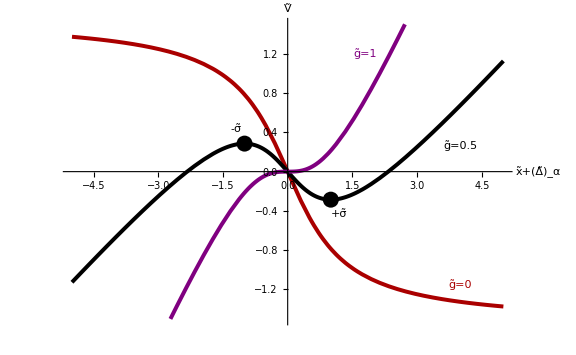

```mathematica
gList={0,0.5,1};
xRange=5;
colorScheme="SouthwestColors";
g0Colour=Darker[Red](*RGBColor[0.368417, 0.506779, 0.709798]*);
g05Colour=Black;
g1Colour=Purple;(*RGBColor[0.880722, 0.611041, 0.142051];*)
sliceColours={{Thickness[0.005],g0Colour},{Thickness[0.005],g05Colour},{Thickness[0.005],g1Colour}};
labelColors={g0Colour,g05Colour,g1Colour};
labels=MapThread[{Text[StringJoin["g̃=",ToString@#1],#2]}&,{gList,{{4,-1.15},{4,0.27},{1.8,1.2}}}];

potentialSlices=g x-ArcTan[x]/.g->gList;
potentialSlicesPlot=Plot[potentialSlices,{x,-xRange,xRange},AxesLabel->{"x̃+(Δ̃)_α","Ṽ"},AxesStyle->Thick,LabelStyle->labelStyle,ImageSize->Large,PlotStyle->sliceColours,PlotRange->{All,{-1.5,1.5}},ImageSize->Large,Ticks->None,Epilog->Join[{Directive[FontSize->25,FontFamily->"Cambria"],{PointSize[0.02],Point[{χ,g χ-ArcTan[χ]}//.{g->0.5,χ->√(1/g-1)}]},Text["+σ̃",{χ+0.2,g χ-ArcTan[χ]-0.15}//.{g->0.5,χ->√(1/g-1)}],Text["-σ̃",{χ-0.2,g χ-ArcTan[χ]+0.15}//.{g->0.5,χ->-√(1/g-1)}],PointSize[0.02],Point[{χ,g χ-ArcTan[χ]}//.{g->0.5,χ->-√(1/g-1)}]},Transpose@{labelColors,labels}]]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["figAdiaPotential.png",Rasterize[potentialSlicesPlot,ImageResolution->300]];
```

### Fig 2b Full dimensionless potential

```mathematica
xRange=5;
potential3DPlot=Plot3D[g x-ArcTan[x],{x,-xRange,xRange},{g,0,1},ColorFunction->"StarryNightColors",AxesLabel->{"x̃+(Δ̃)_α","g̃","Ṽ"},PlotRange->{{-xRange,xRange},{0,1},{-2,2}},LabelStyle->labelStyle,ImageSize->Large,Ticks->{{-4,-2,0,2,4},Automatic,{-2,0,2}},ClippingStyle->None];
tracePlotStyle={Thick,Black,Dashed};
deltaPlusTrace=ParametricPlot3D[{√(1/g-1),g,g(√(1/g-1))-ArcTan[√(1/g-1)]},{g,0.001,1-0.01},PlotStyle->{Thick,Black,Dashed}];
deltaMinusTrace=ParametricPlot3D[{-√(1/g-1),g,g(-√(1/g-1))-ArcTan[-√(1/g-1)]},{g,0.001,1-0.01},PlotStyle->{Thick,Black,Dashed}];
eps=0.01;
g05Trace=ParametricPlot3D[{χ,g,g χ-ArcTan[χ]}/.g->0.5,{χ,-xRange,xRange},PlotStyle->{Thickness[0.01],g05Colour}];
g0Trace=ParametricPlot3D[{χ,g+eps,g χ-ArcTan[χ]}/.g->0,{χ,-xRange,xRange},PlotStyle->{Thickness[0.01],g0Colour}];
g1Trace=ParametricPlot3D[{χ,g-eps,g χ-ArcTan[χ]}/.g->1,{χ,-xRange,xRange},PlotStyle->{Thickness[0.01],g1Colour}];
fullPotentialPlot=Show[potential3DPlot,deltaPlusTrace,deltaMinusTrace,g0Trace,g05Trace,g1Trace,PlotRangePadding->0.02]
```

-Graphics3D-

```mathematica
SetDirectory@NotebookDirectory[];
Export["figAdiaPotentialFull.pdf",fullPotentialPlot];
```

### Fig 3c Dimensionless frequency of oscillation

```mathematica
(*  Dimensionless potential *)
v[x_,g_]:=g x-ArcTan[x];
vPrime[x_,g_]:=D[v[x,g],x];

(* Search to the right for a root *)
FindRight[xstart_,g_,xmax_:50]:=
Module[{vstart,xfound,sol},
vstart=v[xstart,g];
xfound=∞;

sol=NDSolve[{{V'[x]==vPrime[x,g],V[xstart]==vstart},WhenEvent[v[x,g]>vstart,xfound=x;"StopIntegration"]},V,{x,xstart,xmax}];
xfound
]

dx=0.025; (* Size of position grid *)
dg=0.005; (*g Value to look at *)
eps=10^-10;

gList=Range[dg+eps,1-eps,dg];
periodList[gVal_]:=
Quiet@Module[{xLList,xRList,xList,ℰList,AmplitudeList,fList,g=gVal},

xLList=Range[-(√(1-g))/(√g)+eps,+(√(1-g))/(√g)-eps,dx];
xRList=FindRight[#,g]&/@xLList;
xList=Select[Transpose[{xLList,xRList}],Max[#]<∞&];

xLList=First@Transpose@xList;
xRList=Last@Transpose@xList;
ℰList=v[#,g]&/@xLList;
AmplitudeList=xRList-xLList;

fList=MapThread[(√2 Chop@NIntegrate[1/(√(eps+#3-v[x,g])),{x,#1,#2}])^-1&,{xLList,xRList,ℰList}];
Transpose[{g+0*Range[1,Length@fList,1],AmplitudeList,fList}]
];
```

```mathematica
frequencies=Flatten[ParallelMap[periodList,gList],1];
SetDirectory@NotebookDirectory[]
Export["frequencies.mx",frequencies,"MX"]
```

C:\Users\ruvil\OneDrive\Ruvi\Schoolwork\ANU\PhD\Projects\Levitating Mirror\Papers\PTStabilisationPaper\Code\fig2_Adiabatic

frequencies.mx

```mathematica
SetDirectory@NotebookDirectory[];
frequencies=Import["frequencies.mx"];
```

```mathematica
maxAmplitudes={#[[1]],Min[#[[2]],15]}&/@Table[{g,FindRight[-(√(1-g))/(√g),g]+(√(1-g))/(√g)},{g,gList}];
MaxAmp=Interpolation[maxAmplitudes];

freqs=Last/@frequencies;
minFreq=Min@freqs
maxFreq=Max@freqs
```

0.00324732

0.129792

```mathematica
labelStyle=Directive[FontSize->35,FontColor->Black,FontFamily->"Times New Roman"];
labels=Quiet@RegionPlot[Null,{g,0,1.05},{A,0,12},PlotRange->{{0,1},{0,10}},FrameLabel->{"g̃","Oscillation Amplitude (ℓ)"},LabelStyle->labelStyle,ImageSize->Large];
whiteBlock=Quiet@RegionPlot[A>MaxAmp[g],{g,0,1.05},{A,0,12},PlotStyle->White,BoundaryStyle->None];
freqDensityPlot=ListDensityPlot[frequencies,ColorFunction->Function[f,ColorData["BlueGreenYellow"][(f-minFreq)/(maxFreq-minFreq)]],ColorFunctionScaling->False,PlotRange->{{0,1},{0,10}}];
```

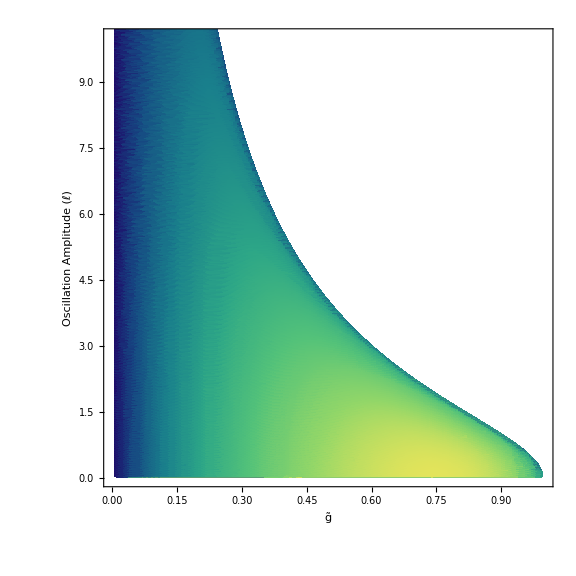

```mathematica
freqLegend=BarLegend[{"BlueGreenYellow",{minFreq,maxFreq}},LegendLabel->"Frequency (ν^-1)",LabelStyle->labelStyle,LegendMarkerSize->500];
frequencyPlot=Row@{Show[labels,freqDensityPlot,whiteBlock],freqLegend}
```

```mathematica
frequencyPlotRastered=Rasterize[frequencyPlot,ImageResolution->150];
SetDirectory@NotebookDirectory[];
Export["figFrequencies.pdf",frequencyPlotRastered];
```